```mathematica
Solve[{Sin[x]==T},x]
```

{{x→ConditionalExpression[π-ArcSin[T]+2 π C[1],C[1]∈Integers]},{x→ConditionalExpression[ArcSin[T]+2 π C[1],C[1]∈Integers]}}

```mathematica
x2[T_]=x/.{x->ConditionalExpression[π-ArcSin[T]+2 π C[1],C[1]∈Integers]}/.C[1]->0
```

π-ArcSin[T]

```mathematica
x1[T_]=x/.{x->ConditionalExpression[ArcSin[T]+2 π C[1],C[1]∈Integers]}/.C[1]->0
```

ArcSin[T]

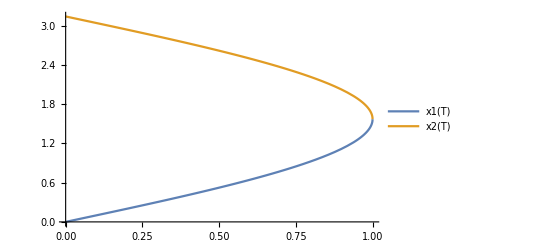

```mathematica
Plot[{x1[T],x2[T]},{T,0,1},PlotLegends->"Expressions"]
```